Checking Sin[x] plotted against spline; restricted to the interval [Pi/2, Pi]

```mathematica
vars={((16-4*Pi)/Pi^3),((-36+8*Pi)/Pi^2),((24+5*Pi)/Pi),(-4+Pi)}
```

{(16-4 π)/π^3,(-36+8 π)/π^2,(24+5 π)/π,-4+π}

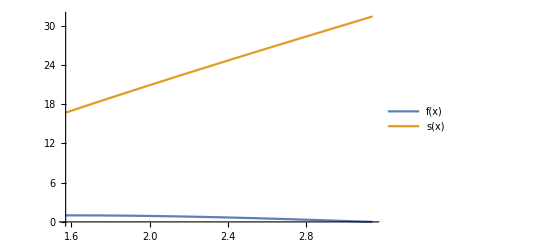

```mathematica
f[t_]:=Sin[t] ;
s[t_]:=(vars[[1]])*t^3+(vars[[2]])*t^2+(vars[[3]])*t+vars[[4]];
Plot[{f[x],s[x]},{x,Pi/2, Pi},PlotLegends->"Expressions"]
```